# TD

play

```mathematica
Np=2000
k=1.38x10^-23
me=9.109x10^-31
hbar=1.055x10^-34
ec=1.602x10^-19
Uh=13.6*ec
```

2000

1.38/x10^23

9.109/x10^31

1.055/x10^34

1.602/x10^19

21.7872/x10^19

```mathematica
tc=(2*Pi*me*k/(hbar^2))^(3/2)
sh[x_,T_,V_]:=x^2-(1-x)*V*T^(3/2)*Exp[-Uh/(k*T)]
```

597.774 (x10^14)^(3/2)

```mathematica
ans=Solve[sh[x,T,1]== 0,x]
```

{{x→0.5 (-1. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)-1. √(4. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.5757 x10^4)/T) T^3))},{x→0.5 (-1. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+√(4. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.5757 x10^4)/T) T^3))}}

```mathematica
Solve[sh[x,200,1],x]
```

```mathematica
ans[[1]]
```

```mathematica
sh[x,100,1]
```

Solve::naqs: -1000 ⅇ^(-0.157878 x10^4) (1-x)+x^2 is not a quantified system of equations and inequalities.

Solve::naqs: A (1-x)+x^2 is not a quantified system of equations and inequalities.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

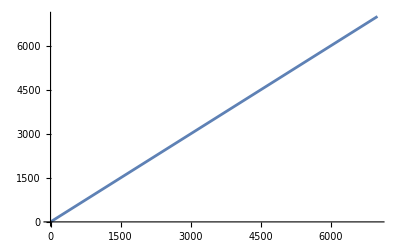

```mathematica
Plot[T/. Solve[sh[x,T]==0.06366,x],{T,0,7000}]
```

```mathematica
Evaluate[T->100,ans[[1]]]
```

Sequence[T→100,{x→0.5 (-1. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)-1. √(4. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.5757 x10^4)/T) T^3))}]

```mathematica
nx[T_]:= 0.5 (-1. ⅇ^(-(15.787826086956526 x10^4)/T) T^(3/2)-1. √(4. ⅇ^(-(15.787826086956526 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.575652173913053 x10^4)/T) T^3))
```

```mathematica
Table[Simplify[Evaluate[nx[100]]],1]
```

```mathematica
numbers={5,1,3,2,1,3,2}
RepFac[n_Integer]:=Module[{result=1,i},For[i=1,i<=n,i++,result=result*i;];
result]

(*Compute the factorial of 5*)
RepFac[5]
```

```mathematica
{5,2,2,2,1,3,2}
```

120

```mathematica
res=numbers[[Length[numbers]]]
```

2

```mathematica
res=numbers[[Length[numbers]]]
```

2

```mathematica
ContSum[numlist_]:= Module[  {result=numbers[[Length[numbers]]],i},   For[i=Length[numbers-1],i>1,i--, result=numbers[[i-1]]+(1/result)];result   ]
```

```mathematica
ContSum[numbers]
```

629/109

```mathematica
Evaluate[%]
```

629/109

```mathematica
N[629/109,25]
```

5.770642201834862385321101

{-500. ⅇ^(-0.157878 x10^4)-0.5 √(1.×10^6 ⅇ^(-0.315757 x10^4)+4000. ⅇ^(-0.157878 x10^4))}

```mathematica
(*Define parameters and initial conditions*)xMin=0.01
xMax=10;
tMax=1;
a=2;
initialCondition[x_]:=Exp[-x] (*Example initial condition*)

(*Define the Kompaneets equation*)
kompaneetsEquation=D[n[t,x],t]==(1/x^2) D[x^4 (a*D[n[t,x],x]+n[t,x]+n[t,x]^2),x];

(*Solve the PDE numerically*)
solution=NDSolve[{kompaneetsEquation,n[0,x]==initialCondition[x],n[t,xMin]==initialCondition[xMin],n[t,xMax]==initialCondition[xMax]},n,{t,0,tMax},{x,xMin,xMax}];

(*Plot the solution*)
Plot3D[Evaluate[n[t,x]/. solution],{x,xMin,xMax},{t,0,tMax},PlotRange->All,AxesLabel->{"x","t","n(t, x)"},PlotLabel->"Solution of the Kompaneets Equation"]
```

0.01

NDSolve::eerr: Warning: scaled local spatial error estimate of 149.678 at t = 1. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 35 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

-Graphics3D-